# Javier Salazar 1001144647

## Project 8.

1.  Area by Monte Carlo 

(a)  Plot Sin[Sin[Sin[Sin[π x]]]]  and  Sin[π x] on the single graph on the interval [0,1]
(b)  Compute the area between Sin[Sin[Sin[Sin[π x]]]] and  Sin[π x] using Monte Carlo for n =1,000,000
(c)  Compare the simulated value with the value obtained from NIntegrate[.]
(d)  Plot the simulated  sample of n =10,000 points

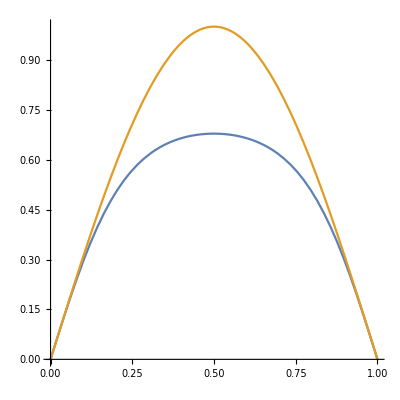

Monte Carlo approximation = 0.14881

True Value = 0.148108

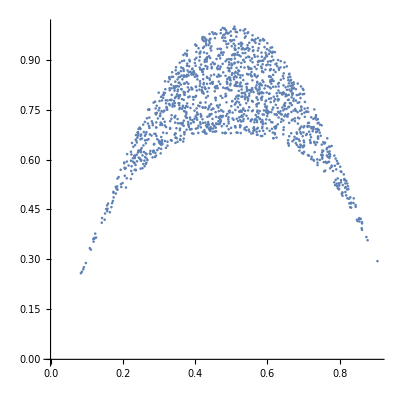

```mathematica
Plot[{Sin[Sin[Sin[Sin[π x]]]],Sin[π x]},{x,0,1},AspectRatio->1]
pie1[n_]:=(hits=0;Do[{x,y}={RandomReal[{0,1}],RandomReal[{0,1}]};If[ Sin[Sin[Sin[Sin[π x]]]]≤y≤Sin[π x],hits=hits+1],{i,1,n}]; hits/n//N)
Print[ "Monte Carlo approximation = ",pie1[1000000]]
TrueValue:=NIntegrate[Sin[π x]-Sin[Sin[Sin[Sin[π x]]]],{x,0,1}]
Print[ "True Value = ",TrueValue]
pie2[n_]:=(hitsCount=0;hitsPoints={};Do[{x,y}={RandomReal[{0,1}],RandomReal[{0,1}]};If[ Sin[Sin[Sin[Sin[π x]]]]≤y≤Sin[π x],hitsCount=hitsCount+1; hits=AppendTo[hitsPoints,{x,y}]],{i,1,n}];4 hitsCount/n//N)
pie2[10000];
ListPlot[hitsPoints,AspectRatio->1]
```

2. Integrals by standard Monte Carlo 

Pick your favorite definite integral on [0,1] whose exact values involve   π  or  ⅇ . Plot the graph of the corresponding function.  Simulate the approximate integral value by using Monte Carlo for n = 1,000,000 and compare the with  exact value or the value obtained by numerical integration NIntegrate[.].

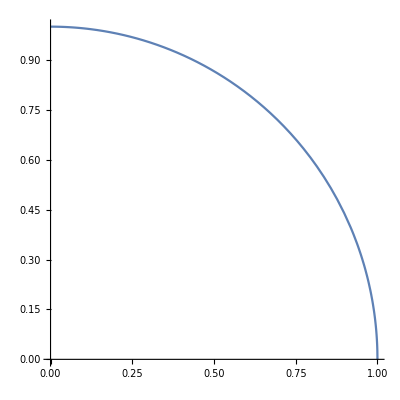

Monte Carlo approximation = 3.14201

True Value = 3.14159

```mathematica
Plot[√(1-x^2),{x,0,1},AspectRatio->1]
pie1[n_]:=(hits=0;Do[{x,y}={RandomReal[{0,1}],RandomReal[{0,1}]};If[ x^2+y^2≤1,hits=hits+1],{i,1,n}]; hits/n//N)
Print[ "Monte Carlo approximation = ",4*pie1[1000000]]
Print[ "True Value = ",π//N]
```

3. Integrals by Importance Sampling Monte Carlo
 
Let  f (x) = 4 √(1-x^2) and   I  = ∫_0^1 f(x)dx .  Find a linear probability density  φ(x) = a x + b  that works 
well with Importance Sampling method of approximating  the integral  I.  Namely, find a and b such that

Var(J_n(φ)) =   1/n(∫_0^1 (f^2(x))/(φ(x))dx  - I^2)  is as small as possible.  That is,  find  a  and  b  which
   
minimize       ∫_0^1 ((4 √(1-x^2))^2)/(a x + b)dx                       (or is close to minimum by numerical approximation) 


(*)  subject to:    a x + b  > 0    and     ∫_0^1 (a x+b) dx   = 1   

Hint. Use  a + 2 (1 - a) x  as parametrization for  a x + b.

Compare the variance for the standard Monte Carlo  Var(J_n(1)) = 1/n(∫_0^1 f^2(x)dx  - I^2)  with the variance  
of the Importance Sampling  Var(J_n(φ))  =  1/n(∫_0^1 (f^2(x))/(φ(x))dx  - I^2) , by taking their ratio and interpret how 
many trials  m  <  n  (by what factor) are sufficient for Importance Sampling to match the accuracy of 
the standard Monte Carlo.

Simulate  m  <  n = 1,000,000 trials of Importance Sampling with your φ(x)  to approximate the integral I  and compare with the standard Monte Carlo simulation corresponding to uniform distribution.

```mathematica
s=0; n=1000000;     (* standard sampling  ~ uniform distribution on [0,1] *)
Do[s=s+f[RandomReal[]],{n}];
a=MonteCarloIntegral=s/n//N;
exact=π//N;
Print["exact = ",exact]
Print["Monte Carlo = ",a]
Print["error = ", Abs[a-exact]]
```

exact = 3.14159

Monte Carlo = 3.14164

error = 0.0000506955

```mathematica
f[x_]:=4 √(1-x^2)       (* 0 ≤ x ≤ 1 *)
φ[x_]:=1.7-1.4x;    g[x_]:=f[x]/φ[x];
Clear[y]
Solve[1.7x- 0.7 x^2 ==y,x]   ;           (* 0 ≤ x ≤ 1 *)
H[u_]:=0.0714286(17-√(289-280u));   
s=0; n=200000; (* importance sampling ~ density φ[x] on [0,1] *)
Do[s=s+g[H[RandomReal[]]],{n}];
a=MonteCarloIntegral=s/n//N;
exact=π//N;
Print["exact = ",exact]
Print["Monte Carlo = ",a]
Print["error = ", Abs[a-exact]]
Print["Importace sampling takes about 5x less iterations"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

exact = 3.14159

Monte Carlo = 3.14316

error = 0.00156335

Importace sampling takes about 5x less iterations

4. Generate a sample of 10,000 from a random variable X on {1, 2, . . . , 20} with probability distribution P(X = k ) = k/210  and plot together the graph of obtained frequencies versus the exact distribution of  X.  Find the expected number of trials to generate 10,000 accepted outcomes.

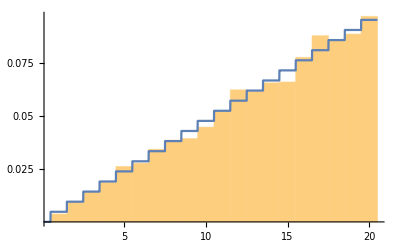

1.93311

1.90476

```mathematica
Clear[u,i,p]
p={1/210,2/210,3/210,4/210,5/210,6/210,7/210,8/210,9/210,10/210,11/210,12/210,13/210,14/210,15/210,16/210,17/210,18/210,19/210,20/210};
simu1={};
Do[{i=RandomInteger[{1,20}],u=RandomReal[],If[u≤p[[i]]/(20/210),AppendTo[simu1,i]]},{10000}]
g1=Histogram[simu1,{0.5,20.5,1},"Probability",Ticks->{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{.025,.05,.075,.1,.125,0.15}}];
g2=Plot[Piecewise[{{1/210,0.5≤x<1.5},{2/210,1.5≤x<2.5},{3/210,2.5≤x<3.5},{4/210,3.5≤x<4.5},{5/210,4.5≤x<5.5},{6/210,5.5≤x<6.5},{7/210,6.5≤x<7.5},{8/210,7.5≤x<8.5},{9/210,8.5≤x<9.5},{10/210,9.5≤x<10.5},{11/210,10.5≤x<11.5},{12/210,11.5≤x<12.5},{13/210,12.5≤x<13.5},{14/210,13.5≤x<14.5},{15/210,14.5≤x<15.5},{16/210,15.5≤x<16.5},{17/210,16.5≤x<17.5},{18/210,17.5≤x<18.5},{19/210,18.5≤x<19.5},{20/210,19.5≤x<20.5}}],{x,0,20.5}];
Show [g1,g2]  (* blue is the exact distribution of p, histogram of the simualted data is yellow *)
10000/Length[simu1]//N
400/210//N
```

5. Generate a sample of 10,000 from a random variable X  on [0, 2] with density f(x) = 3/2 x (x-1)^2  for 
g = 1/2  ~ U[0,2]  and another g(x) of choice that improves the acceptance rate.  Plot together the graph of obtained frequencies versus density f(x). Compare in both cases the average number of trials needed per acceptance to the theoretical average acceptance rate = c.

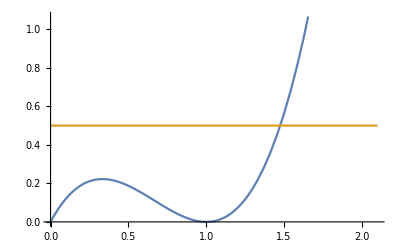

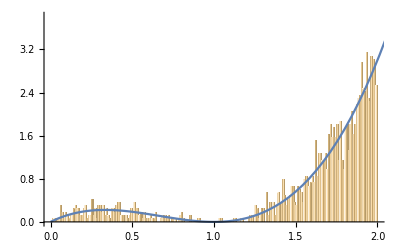

6.035

```mathematica
f[x_]:=3/2 x(x-1)^2;g[x_]:=1/2;c=6;
Plot[{f[x],g[x]},{x,0,2.1}] 
simu2={};
Do[y=RandomReal[{0,2}];u=RandomReal[];If[ u≤1/2 y(y-1)^2,AppendTo[simu2,y]],{10000}]
Show[Histogram[simu2,{0,2,0.01},"ProbabilityDensity",ChartElementFunction->"GlassRectangle"],Plot[f[x],{x,0,2.1}]]
10000/Length[simu2]//N
```

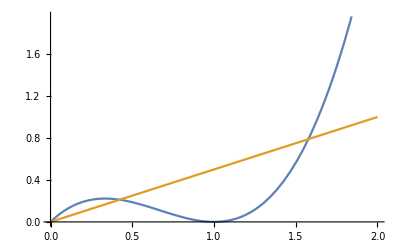

1.98926

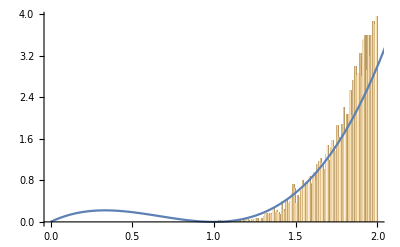

```mathematica
f[x_]:=3/2 x(x-1)^2;g[x_]:=1/2 x;c=3;
Plot[{f[x],g[x]},{x,0,2}] 
simu3={};
Do[y=Sqrt[RandomReal[]]+1;u=RandomReal[];If[ u≤(y-1)^2,AppendTo[simu3,y]],{10000}]
10000/Length[simu3]//N
Show[Histogram[simu3,{0,2,0.01},"ProbabilityDensity",ChartElementFunction->"GlassRectangle"],Plot[f[x],{x,0,2.1}]]
```